```mathematica
Входные данные;
```

```mathematica
ϵ=0.001;X0={-1,-2};α=1;(* X0={√10,0}; *)
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2; (*11 x^2+3 y^2+6x y -2 √10 (x-3y)-22;*)
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
HesseF[{x1_,y1_}] :=( Grad[Grad[f[{x,y}],{x,y}],{x,y}])/.{x->x1,y->y1};
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
wArray={};
κArray={};
Clear[κ,ka, kap]
```

```mathematica
Метод Давидона- Флетчера - Пауэлла;
```

Результат получен за 7 итер.: X = {0.999996, 0.999974}

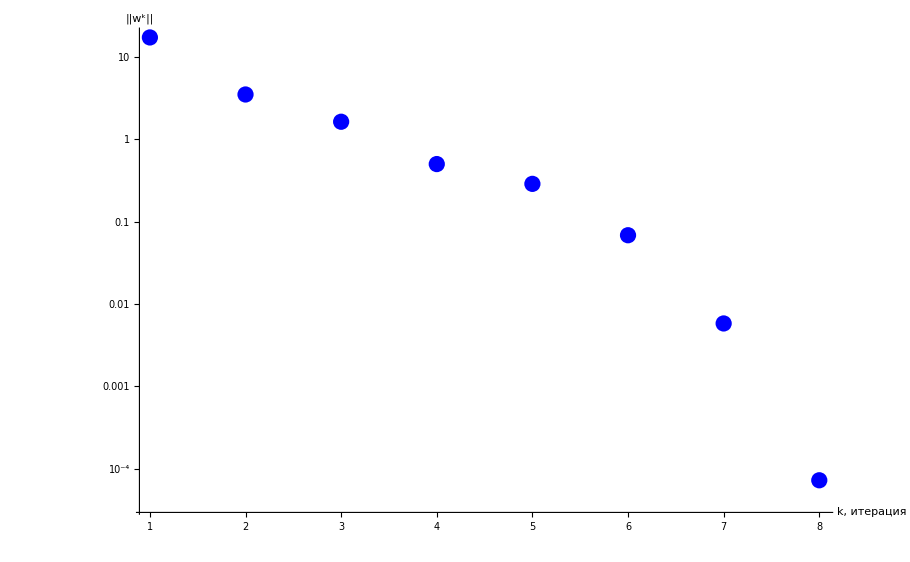

```mathematica
A=IdentityMatrix[2];
w=antiGradF[X];wArray=Append[wArray,w];
While[norm[[-1]]≥ ϵ,
p=A.w;
p=p/Norm[p];
κ = NArgMin[f[X+kap p],kap];κArray=Append[κArray,κ];
X=X+κ p;
points=Append[points,X];fValues=Append[fValues,f[X]];
w=antiGradF[X];wArray=Append[wArray,w];norm=Append[norm,NormGradF[X]];
dX=points[[-1]]-points[[-2]]; dw=wArray[[-1]] - wArray[[-2]];
ΔA=N[(-TensorProduct[dX,dX])/(dw.dX)-(A.TensorProduct[dw,dw].A)/((A.dw).dw)];
A=A+ΔA;

];



(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

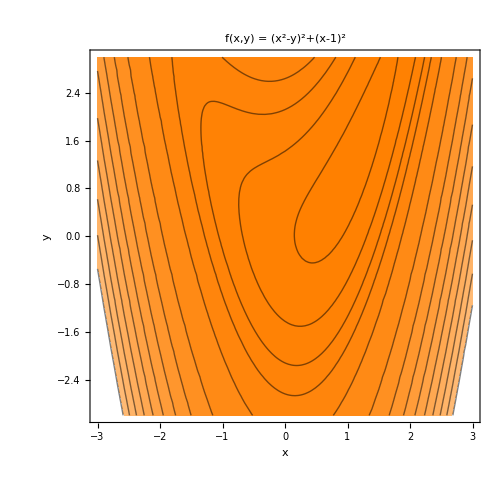

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500]
```

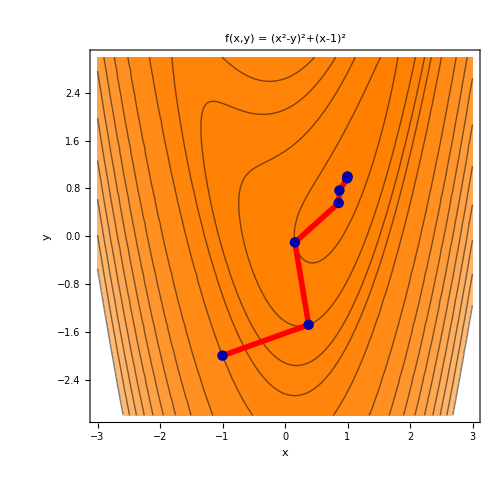

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13.0000000 | 17.088007
1 | ( 0.3785554, -1.4830417 ) | 3.0311944 | 3.4738764
... | ... | ... | ...
2 | ( 0.1583387, -0.1027526 ) | 0.7247327 | 1.6226301
3 | ( 0.8592963, 0.5572941 ) | 0.0525933 | 0.4974938
4 | ( 0.8707394, 0.7660215 ) | 0.0167697 | 0.2862376
5 | ( 0.9942035, 0.9708453 ) | 0.0003432 | 0.0681664
6 | ( 0.9979770, 0.9963821 ) |       -6
4.3 10 | 0.0058008
7 | ( 0.9999961, 0.9999743 ) |      -8
0. 10 | 0.0000726

```mathematica
Метод Бройдена - Пауэлла - Гольдфарба - Шенно;
```

Результат получен за 7 итер.: X = {0.999996, 0.999974}

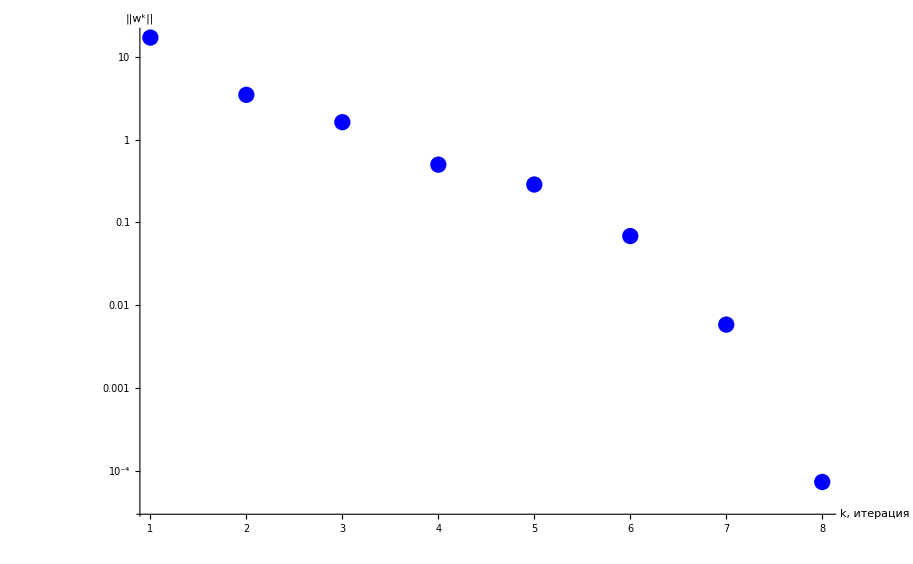

```mathematica
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
wArray={};
μ =0.5;
Clear[κ]

A=IdentityMatrix[2];
w=antiGradF[X];wArray=Append[wArray,w];
While[norm[[-1]]≥ ϵ,
p=A.w;
p=p/Norm[p];
κ = NArgMin[f[X+ka p],ka];κArray=Append[κArray,κ];
X=X+κ p;
points=Append[points,X];fValues=Append[fValues,f[X]];
w=antiGradF[X];wArray=Append[wArray,w];norm=Append[norm,NormGradF[X]];
dX=points[[-1]]-points[[-2]]; dw=wArray[[-1]] - wArray[[-2]];
r=(A.dw)/((A.dw).dw)-dX/(dw.dX);
ΔA=N[(-TensorProduct[dX,dX])/(dw.dX)-(A.TensorProduct[dw,dw].A)/((A.dw).dw)+(A.dw).dw TensorProduct[r,r]];
A=A+ΔA;

];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

-Graphics-

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
For[i=1,i≤len,i++,gridData[[i,4]]=ToString[SetAccuracy[κArray[[i]],8]]];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13.0000000 | 1.4722979 | 17.088007
1 | ( 0.3785554, -1.4830417 ) | 3.0311944 | 1.3977458 | 3.4738764
... | ... | ... | ... | ...
2 | ( 0.1583387, -0.1027527 ) | 0.7247327 | 0.9628100 | 1.6226301
3 | ( 0.8592963, 0.5572941 ) | 0.0525933 | 0.2090409 | 0.4974938
4 | ( 0.8707394, 0.7660215 ) | 0.0167697 | 0.2391572 | 0.2862375
5 | ( 0.9942035, 0.9708453 ) | 0.0003432 | 0.0258141 | 0.0681664
6 | ( 0.9979770, 0.9963821 ) |       -6
4.3 10 | 0.0041208 | 0.0058008
7 | ( 0.9999961, 0.9999743 ) |      -8
0. 10 | 1.4722979 | 0.0000726

```mathematica
Метод Пауэлла;
```

Результат получен за 7 итер.: X = {0.999996, 0.999974}

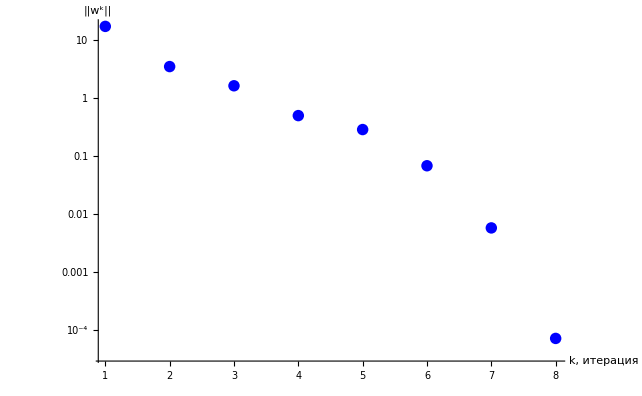

```mathematica
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
wArray={};
μ =0.5;
Clear[κ]

A=IdentityMatrix[2];
w=antiGradF[X];wArray=Append[wArray,w];
While[norm[[-1]]≥ ϵ,
p=A.w;
p=p/Norm[p];
κ = NArgMin[f[X+ka p],ka];κArray=Append[κArray,κ];
X=X+κ p;
points=Append[points,X];fValues=Append[fValues,f[X]];
w=antiGradF[X];wArray=Append[wArray,w];norm=Append[norm,NormGradF[X]];
dX=points[[-1]]-points[[-2]]; dw=wArray[[-1]] - wArray[[-2]];
dXn=dX+A.dw;
ΔA=N[(-TensorProduct[dXn,dXn])/(dw.dXn)];
A=A+ΔA;

];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

-Graphics-

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13.0000000 | 17.088007
1 | ( 0.3785554, -1.4830417 ) | 3.0311944 | 3.4738764
... | ... | ... | ...
2 | ( 0.1583387, -0.1027527 ) | 0.7247327 | 1.6226301
3 | ( 0.8592963, 0.5572941 ) | 0.0525933 | 0.4974938
4 | ( 0.8707394, 0.7660215 ) | 0.0167697 | 0.2862375
5 | ( 0.9942035, 0.9708453 ) | 0.0003432 | 0.0681664
6 | ( 0.9979770, 0.9963821 ) |       -6
4.3 10 | 0.0058008
7 | ( 0.9999961, 0.9999743 ) |      -8
0. 10 | 0.0000726

```mathematica
Метод Мак-Кормика;
```

Результат получен за 10 итер.: X = {0.999793, 0.999499}

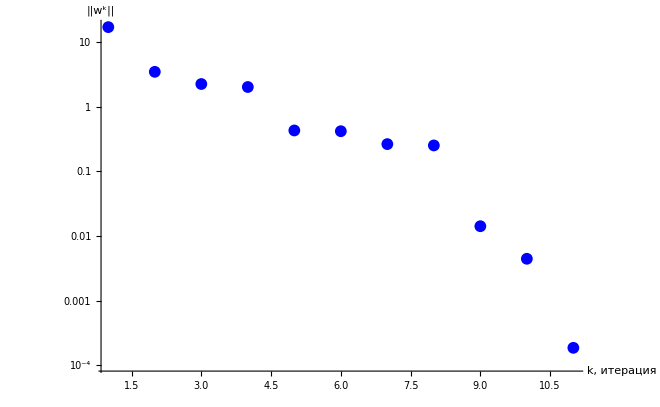

```mathematica
Clear[κ,X,points,norm,wArray,κArray,Xpos,w,A,ΔA,dX,dw,p];
X=X0;
points={X0};
norm={NormGradF[X0]};
fValues={f[X0]};
pArray={};
wArray={};κArray={};
 ω=0.4;
κ=0.5;

A=IdentityMatrix[2];
w=antiGradF[X];wArray=Append[wArray,w];
count=1;
While[norm[[-1]]≥ ϵ,
count++;If[count>10,{A=IdentityMatrix[2];count=1},1];
p=A.w;
p=p/Norm[p];
κ = NArgMin[f[X+ka p],ka];κArray=Append[κArray,κ];
X=X+κ p;

points=Append[points,X];fValues=Append[fValues,f[X]];
w=antiGradF[X];wArray=Append[wArray,w];norm=Append[norm,NormGradF[X]];
dX=points[[-1]]-points[[-2]]; dw=wArray[[-1]] - wArray[[-2]];
ΔA=(-KroneckerProduct[(dX+A.dw),dX])/(dw.dX);
A=A+ΔA;

];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

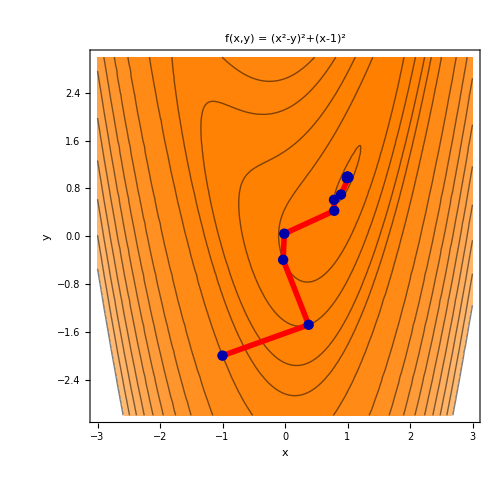

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[3]],fValues[[6]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;6]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13.0000000 | 17.088007
1 | ( 0.3785554, -1.4830417 ) | 3.0311944 | 3.4738764
2 | ( -0.0297935, -0.3941112 ) | 1.2164987 | 2.2499145
3 | ( -0.0113931, 0.0426938 ) | 1.0247278 | 2.0226387
4 | ( 0.7878727, 0.4270048 ) | 0.0825326 | 0.4299421
... | ... | ... | ...
5 | ( 0.7841666, 0.6106963 ) | 0.0466019 | 0.418512
6 | ( 0.8958598, 0.6987624 ) | 0.0216201 | 0.2643744
7 | ( 1.0163717, 0.9839324 ) | 0.0026768 | 0.2521626
8 | ( 0.9897165, 0.9729831 ) | 0.0001487 | 0.0141743
9 | ( 0.9994344, 0.9996302 ) |      -7
9. 10 | 0.0044424
10 | ( 0.9997933, 0.9994993 ) |      -7
0. 10 | 0.0001861